## Funciones dieléctricas de eritrocitos

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Importación de paquetes

```mathematica
Needs["MaTeX`"]
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
Needs["MaTeX`"] (*Importa la paquetería de LaTeX*)
SetOptions[MaTeX, "Preamble" -> {"\\usepackage{xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["KramersKronig`"]
Needs["MieTheory`"]
Needs["GoldenSectionSearchMaxMin`"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

omega10=Range[0,10,0.01]; 
omegaVis=Range[2,3.1,0.01];
energyTicksMajorVisible={2.07,2.26,2.48,2.76,3.1};

epsPlasma=1.823;

(*tolerancia para el GoldenSectionSeach*)
tolRes=1.*^-8;


(*Colores*)
blueUNAM=RGBColor[6/255,151/255,213/255];
redUNAM=RGBColor[232/255,68/255,42/255];
gris=RGBColor[127/255,146/255,151/255];
colors2={blueUNAM, redUNAM}
color5={Orange}
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
```

{RGBColor[Rational[2, 85], Rational[151, 255], Rational[71, 85]],RGBColor[Rational[232, 255], Rational[4, 15], Rational[14, 85]]}

{RGBColor[1, 0.5, 0]}

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

## Gráficas

```mathematica
plotStyling = {PlotRange -> All,
   PlotStyle -> colors,
   Frame -> True,
   FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.8],
   LabelStyle->{FontFamily->"Latin Modern Roman 10"},
   ImagePadding->{{90,20},{60,60}}};


(*Directorio para guardar las figuras*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Congreso-2026\\Figuras"]
```

C:\Users\danal\Documents\Github\Congreso-2026\Figuras

## Funciones generales

```mathematica
epsRe[parteRe_,parteIm_,x_]:=parteRe[x]^2-parteIm[x]^2;
epsIm[parteRe_,parteIm_,x_]:=(2*parteRe[x]*parteIm[x]);
eps[parteRe_,parteIm_,x_]:=(parteRe[x]+I parteIm[x])^2;
```

```mathematica
(*Función para encontrar los máximos alrededor de intervalos dados*)
ω0i[epsFunc_, intervalos_, tolRes_] := GoldenSectionSearchMax[epsFunc, #1, #2, tolRes] & @@@ intervalos;
  
(*Parte imaginaria de lorentziana*)
lorentzIm[omega_,omega0_,gamma_]:=(gamma omega)/((omega0^2-omega^2)^2+(gamma omega)^2)
(*Suma lorentzianas*)
lorentzSumIm[omega_, A_List, omega0_List, gamma_List] :=  Sum[A[[i]] * lorentzIm[omega, omega0[[i]], gamma[[i]]], {i, Length[A]}]
```

## Datos beta y H2O -> Parte real

```mathematica
(*Función que da la parte real del índice de refracción a partir de la relación de Meinke 2006*)
datosH2O=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\H2O_n.csv"];
datosBeta=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\Beta_parameter_ReN_Erythrocytes.csv"];
datos1Beta=Drop[datosBeta,1];
datos1H2O=Drop[datosH2O,1];
datos2Beta=h c/datos1Beta[[All,1]];
datos2H2O=h c/(datos1H2O[[All,1]]*1000);
beta=Interpolation[Transpose[{datos2Beta,datos1Beta[[All,2]]}]]
h2o=Interpolation[Transpose[{datos2H2O,datos1H2O[[All,2]]}]];

(*Se va a encontrar la parte real empleando la relación de Meinke 2006*)
parteRe[x_,C_]:=h2o[x]*((beta[x]*C)+1);
```

InterpolatingFunction[…]

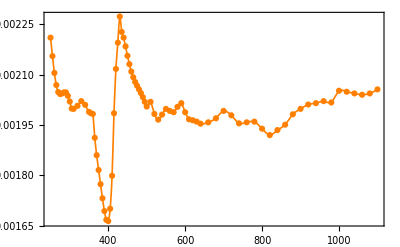

```mathematica
majorTicks=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[200,1100,200]}];

betainterp=Plot[Interpolation[Transpose[{datos1Beta[[All,1]],datos1Beta[[All,2]]}]][λ],{λ,250,1100},PlotStyle -> {Orange,Thickness[0.003]},Evaluate[Sequence @@ plotStyling]];
betaplotpoints=ListPlot[Transpose[{datos1Beta[[All,1]],datos1Beta[[All,2]]}],PlotStyle -> {Orange},Evaluate[Sequence @@ plotStyling]];

betaplot=Show[{betainterp,betaplotpoints}, FrameLabel->{{Style[MaTeX["\\beta(\\lambda)\\:[\\mbox{dL/g}] "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Export["beta.svg",betaplot]
```

beta.svg

## Concentración 15.3 g/dL

### Importación de datos

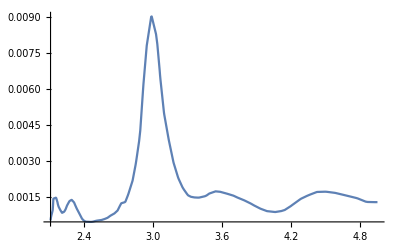

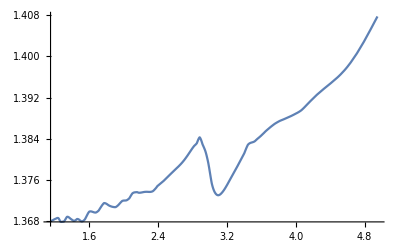

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
datosuA=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\15.3_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uA=Drop[datosuA,1];
datos1uA=Map[ToExpression,datos1uA,{2}];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2im=h c/datos1uA[[All,1]];
(*Obtener la parte imaginaria del índice de refracción a partir del coeficiente de absorción*)
datos3im=((datos1uA[[All,2]]*10^(-6))/(4*Pi))*datos1uA[[All,1]];
(*Se interpolan los datos de la parte imaginaria*)
parteIm15=Interpolation[Transpose[{datos2im,datos3im}],InterpolationOrder->1];
parteRe15[x_]:=parteRe[x,15.3]

Plot[parteIm15[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe15[x],{x,1.15,4.95},PlotRange->All]
```

### Ajuste de lorentzianas

#### Ajuste sin el pico pequeño

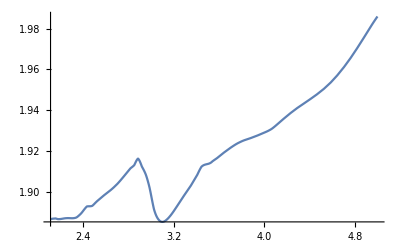

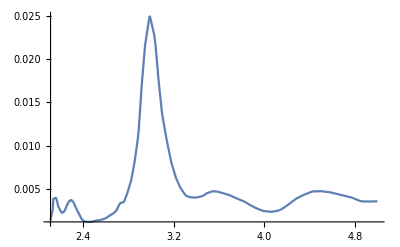

```mathematica
(*Función dieléctrica experimental*)
eps15Im[x_]:=Im[eps[parteRe15,parteIm15,x]];
eps15Re[x_]:=Re[eps[parteRe15,parteIm15,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos15={{2.13,2.15},{2.2,2.3},{2.8,3.2},{3.4,3.7},{4.2,4.7}};

ω0i15=ω0i[eps15Im,intervalos15,tolRes];

Plot[eps15Re[x],{x,2.11,5}]
Plot[eps15Im[x],{x,2.11,5},PlotRange->All]
```

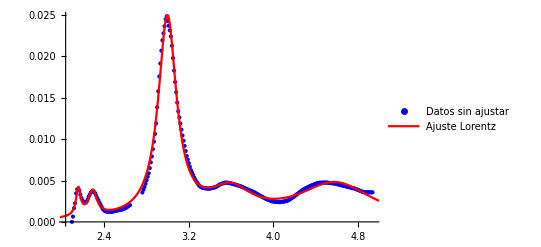

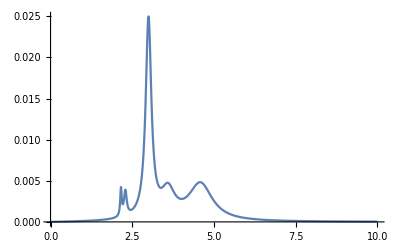

{0.000383064,2.15422,0.0538666,0.000698305,2.28956,0.100709,0.0151476,2.99856,0.20917,0.00602949,3.60037,0.507902,0.0182613,4.60703,0.877683}

```mathematica
(*Datos para ajuste ignorando el pico pequeño faltante*)
{xmin15,xmax15}={Min[datos2im],Max[datos2im]};

eps15Data0=Table[{x,eps15Im[x]},{x,xmin15,2.65,0.01}];
eps15Data1=Table[{x,eps15Im[x]},{x,2.76,xmax15,0.01}];

eps15Data2=Join[eps15Data0,eps15Data1];
eps15Data=Table[{x,eps15Im[x]},{x,xmin15,xmax15,0.01}];

fit15 = NonlinearModelFit[eps15Data2,
                           lorentzSumIm[ω, {A1, A2, A3, A4, A5}, {ω01, ω02, ω03, ω04, ω05}, {γ1, γ2, γ3, γ4, γ5} ], 
             
                          {{A1, 0.01}, {ω01, ω0i15[[1]]}, {γ1, 0.05}, 
                           {A2, 0.01}, {ω02, ω0i15[[2]]}, {γ2, 0.1}, 
                           {A3, 0.01}, {ω03, ω0i15[[3]]}, {γ3, 0.1}, 
                           {A4, 0.01}, {ω04, ω0i15[[4]]}, {γ4, 0.1}, 
                            {A5, 0.01}, {ω05, ω0i15[[5]]}, {γ5, 0.1}}, 
                            ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps15Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fit15[ω],{ω,xmin15-0.5,xmax15+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
              
Plot[fit15[ω],{ω,0,10},PlotRange->All]

fit15Values=Values[fit15["BestFitParameters"]]
```

#### Ajuste pico pequeño

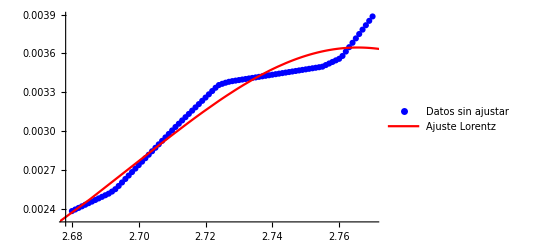

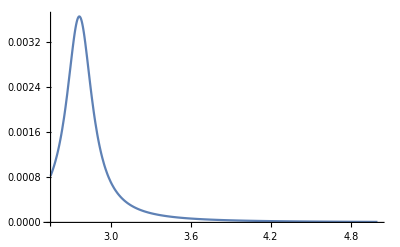

{A1→2.35×10^-3,ω01→2.77,γ1→2.33×10^-1}

{0.00235035,2.76803,0.233036}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps15Data3=Table[{x,eps15Im[x]},{x,2.68,2.77,0.001}];

fit151=NonlinearModelFit[eps15Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.75},{γ1,0.005}},ω];

Show[ListPlot[eps15Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit151[ω],{ω,2.55,3.5},
      PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
      
Plot[fit151[ω],{ω,2.55,5},PlotRange->All]

ScientificForm[fit151["BestFitParameters"],3]
fit151Values=Values[fit151["BestFitParameters"]]
```

#### Ajuste total

```mathematica
fit15tot=NonlinearModelFit[eps15Data,{lorentzSumIm[ω, {A1, A2, A3, A4, A5,A6}, {ω01, ω02, ω03, ω04, ω05,ω06}, {γ1, γ2, γ3, γ4, γ5,γ6} ], 
                         0.002>A6>0 && 0.2>γ6>0 && 2.77>ω06>2.66}, 
                         {{A1,fit15Values[[1]]},{ω01,fit15Values[[2]]},{γ1,fit15Values[[3]]},
                         {A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,fit15Values[[6]]},
                         {A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit15Values[[9]]},
                         {A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},
                         {A5,fit15Values[[13]]},{ω05,fit15Values[[14]]},{γ5,fit15Values[[15]]},
                         {A6,fit151Values[[1]]},{ω06,fit151Values[[2]]},{γ6,fit151Values[[3]]}},
                         ω, Weights->(If[2.6<#<2.8,100,2]&/@(eps15Data[[All,1]]))];

Show[ListPlot[eps15Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
        Plot[fit15tot[ω],{ω,xmin15,xmax15},PlotStyle->{Thick,Red},  
        PlotLegends->{"Ajuste Lorentz"},PlotRange->All]];

Plot[fit15tot[ω],{ω,0,10},PlotRange->All];

ScientificForm[fit15tot["BestFitParameters"],3]
```

{A1→4.13×10^-4,ω01→2.15,γ1→5.61×10^-2,A2→6.65×10^-4,ω02→2.29,γ2→9.02×10^-2,A3→1.39×10^-2,ω03→3.,γ3→1.86×10^-1,A4→6.58×10^-3,ω04→3.59,γ4→5.15×10^-1,A5→1.74×10^-2,ω05→4.6,γ5→8.24×10^-1,A6→1.22×10^-5,ω06→2.72,γ6→6.97×10^-3}

{{250.,4.96},{300.,4.13},{350.,3.54},{400.,3.10},{450.,2.76},{500.,2.48},{550.,2.25},{600.,2.07}}

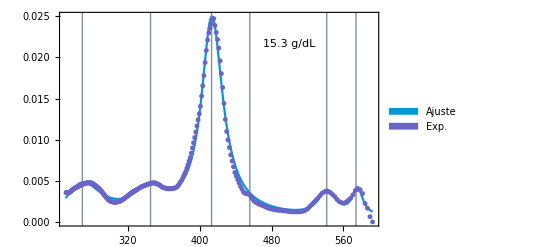

```mathematica
majorTicks15=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[250,600,50]}]

interp15=Plot[fit15[h c/λ],{λ,h c/xmax15,h c/xmin15},PlotStyle->blueUNAM,
              PlotLegends->Placed[SwatchLegend[{Style["Ajuste",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.717,0.65}],
              Epilog->{{gris,InfiniteLine[{{h c/2.16,0},{h c/2.16,1}}]},(*línea en x1*)
                        {gris,InfiniteLine[{{h c/2.29,0},{h c/2.29,1}}]},
                        {gris,InfiniteLine[{{h c/3,0},{h c/3,1}}]},
                        {gris,InfiniteLine[{{h c/3.59,0},{h c/3.59,1}}]},
                        {gris,InfiniteLine[{{h c/4.6,0},{h c/4.6,1}}]},
                        {gris,InfiniteLine[{{h c/2.72,0},{h c/2.72,1}}],
                        Inset[Style["15.3 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]]}(*línea en y=-0.5*)},
              Evaluate[Sequence @@ plotStyling]];
plotpoints15=ListPlot[{h c/#[[1]],#[[2]]}&/@eps15Data,PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                    LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                                    Evaluate[Sequence @@ plotStyling]];

ajuste15=Show[{interp15,plotpoints15}, FrameLabel->{{Style[MaTeX["\\varepsilon''(\\lambda) "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,majorTicks15}}]
```

```mathematica
resonancias={2.15,2.29,2.72,3,3.59,4.6};
majorTicksprueba2=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,resonancias}]
Show[{interp15,plotpoints15}, FrameLabel->{{Style[MaTeX["\\varepsilon''(\\lambda) "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,majorTicksprueba2}}]
```

{{576.671,2.15},{541.416,2.29},{455.824,2.72},{413.281,3},{345.36,3.59},{269.531,4.60}}

-Graphics-

### Parte real vía SSKK

```mathematica
omegaprueba15=Range[2.11,4.94,0.01];
parteIm015=Table[fit15tot[x],{x,omegaprueba15}];
parteIm01510=Table[fit15tot[x],{x,omega10}];

datosRealObjetivo15=eps15Re/@omegaprueba15;
```

```mathematica
parteReSSKK15=sskkrebook[omega10,parteIm01510,2.88,eps15Re[2.88]];
partere152=Interpolation[Transpose[{omega10,parteReSSKK15}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 8.76906×10^-7.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

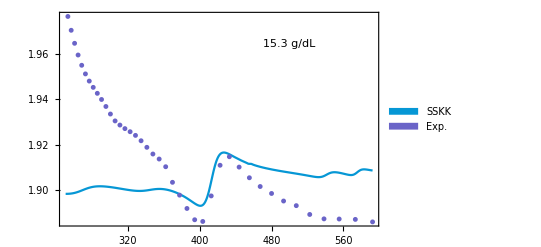

```mathematica
eps15DataRe=Table[{x,eps15Re[x]},{x,xmin15,xmax15,0.07}];

majorTicks15=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[250,600,50]}];

interp15sskk=Plot[partere152[h c/λ],{λ,h c/xmax15,h c/xmin15},
                  PlotStyle->blueUNAM,
                  PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.715,0.63}],
                  Epilog->Inset[Style["15.3 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]],
                  Evaluate[Sequence @@ plotStyling]];

plotpoints15sskk=ListPlot[eps152Re={h c/#[[1]],#[[2]]}&/@eps15DataRe,
                          PlotMarkers->{"●",5},
                          PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                          Evaluate[Sequence @@ plotStyling]];

Show[{interp15sskk,plotpoints15sskk}, FrameLabel->{{Style[MaTeX["\\varepsilon''(\\lambda)"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
                                
                                eps28DataRe=Table[{x,eps15Re[x]},{x,xmin15,xmax15,0.07}];
```

## Concentración 28.7 g/dL

### Importación de datos

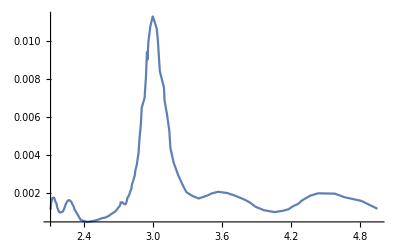

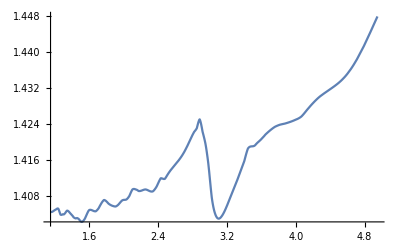

```mathematica
(*Se van a importar los datos de la parte real e imaginaria del índice de refracción*)
datos0Im=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2Im=h c/datos1Im[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
parteIm280=Transpose[{datos2Im,datos1Im[[All,2]]}];
parteIm28=Interpolation[parteIm280,InterpolationOrder->1];

parteRe28[x_]:=parteRe[x,28.7];

Plot[parteIm28[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe28[x],{x,1.15,4.95},PlotRange->All]
```

### Ajuste de lorentzianas

#### Ajuste sin el pico pequeño

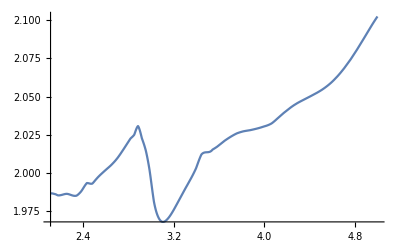

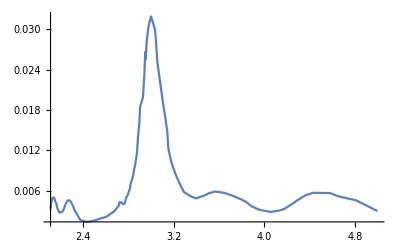

```mathematica
(*Función dieléctrica experimental*)
eps28Im[x_]:=Im[eps[parteRe28,parteIm28,x]];
eps28Re[x_]:=Re[eps[parteRe28,parteIm28,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos28={{2.1,2.2},{2.2,2.4},{2.8,3.3},{3.5,3.8},{4,4.7}};

ω0i28=ω0i[eps28Im,intervalos28,tolRes];

Plot[eps28Re[x],{x,2.11,5}]
Plot[eps28Im[x],{x,2.11,5},PlotRange->All]
```

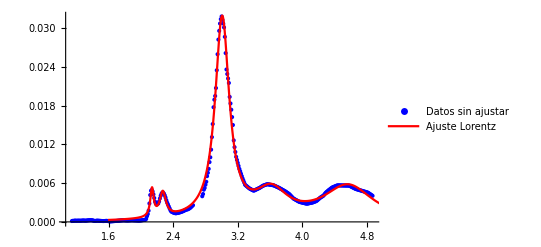

{0.000383064,2.15422,0.0538666,0.000698305,2.28956,0.100709,0.0151476,2.99856,0.20917,0.00602949,3.60037,0.507902,0.0182613,4.60703,0.877683}

```mathematica
(*Datos para ajuste ignorando el pico pequeño faltante*)
{xmin,xmax}={Min[datos2Im],Max[datos2Im]};

eps28Data0=Table[{x,eps28Im[x]},{x,xmin,2.65,0.01}];
eps28Data1=Table[{x,eps28Im[x]},{x,2.76,xmax,0.01}];
eps28Data2=Join[eps28Data0,eps28Data1];

eps28Data=Table[{x,eps28Im[x]},{x,xmin,xmax,0.01}];
eps28DataLambda=Table[{x,eps28Im[h c/x]},{x,datos1Im[[All,1]]}];

fit28 = NonlinearModelFit[eps28Data2,
                           lorentzSumIm[ω, {A1, A2, A3, A4, A5}, {ω01, ω02, ω03, ω04, ω05}, {γ1, γ2, γ3, γ4, γ5} ], 
             
                          {{A1, 0.01}, {ω01, ω0i15[[1]]}, {γ1, 0.05}, 
                           {A2, 0.01}, {ω02, ω0i15[[2]]}, {γ2, 0.1}, 
                           {A3, 0.01}, {ω03, ω0i15[[3]]}, {γ3, 0.1}, 
                           {A4, 0.01}, {ω04, ω0i15[[4]]}, {γ4, 0.1}, 
                            {A5, 0.01}, {ω05, ω0i15[[5]]}, {γ5, 0.1}}, 
                            ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps28Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fit28[ω],{ω,xmin15-0.5,xmax15+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
              
Plot[fit28[ω],{ω,0,10},PlotRange->All];

fit28Values=Values[fit15["BestFitParameters"]]
```

#### Ajuste pico pequeño

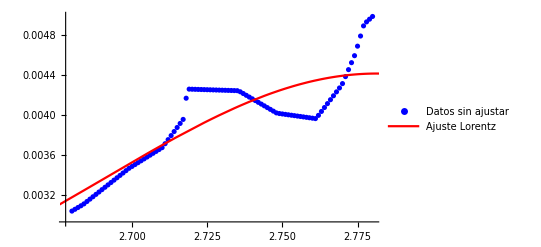

{A1→4.×10^-3,ω01→2.79,γ1→3.25×10^-1}

{0.003998,2.78624,0.325032}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps28Data3=Table[{x,eps28Im[x]},{x,2.68,2.78,0.001}];

fit281=NonlinearModelFit[eps28Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0005},{ω01,2.7},{γ1,0.15}},ω];

Show[ListPlot[eps28Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
        Plot[fit281[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
        
ScientificForm[fit281["BestFitParameters"],3]
fit281Values=Values[fit281["BestFitParameters"]]
```

#### Ajuste total

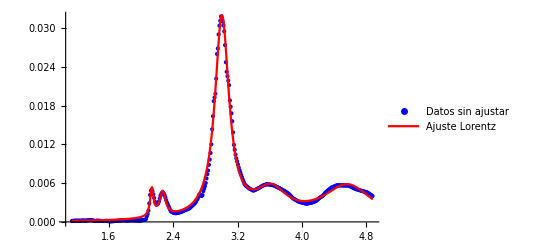

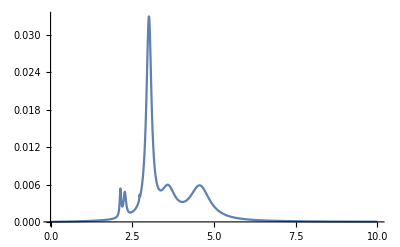

{A1→4.85×10^-4,ω01→2.14,γ1→5.21×10^-2,A2→-8.27×10^-4,ω02→2.27,γ2→-9.33×10^-2,A3→1.8×10^-2,ω03→3.01,γ3→1.87×10^-1,A4→8.45×10^-3,ω04→3.61,γ4→5.23×10^-1,A5→1.84×10^-2,ω05→4.58,γ5→7.38×10^-1,A6→2.55×10^-5,ω06→2.72,γ6→1.31×10^-2}

```mathematica
fit28tot=NonlinearModelFit[eps28Data,{lorentzSumIm[ω, {A1, A2, A3, A4, A5,A6}, {ω01, ω02, ω03, ω04, ω05,ω06}, {γ1, γ2, γ3, γ4, γ5,γ6} ], 
                         0.002>A6>0 && 0.2>γ6>0 && 2.77>ω06>2.66}, 
                         {{A1,fit15Values[[1]]},{ω01,fit15Values[[2]]},{γ1,fit15Values[[3]]},
                         {A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,fit15Values[[6]]},
                         {A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit15Values[[9]]},
                         {A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},
                         {A5,fit15Values[[13]]},{ω05,fit15Values[[14]]},{γ5,fit15Values[[15]]},
                         {A6,fit281Values[[1]]},{ω06,fit281Values[[2]]},{γ6,fit281Values[[3]]}},
                         ω, Weights->(If[2.6<#<2.8,100,2]&/@(eps28Data[[All,1]]))];

Show[ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
          Plot[fit28[ω],{ω,xmin,xmax},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

Plot[fit28tot[ω],{ω,0,10},PlotRange->All]

ScientificForm[fit28tot["BestFitParameters"],3]
```

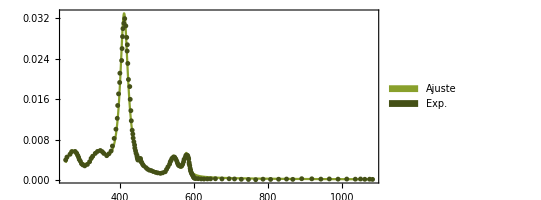

```mathematica
majorTicks28=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,{2.14,2.27,3.01,3.61,4.58,2.72}}];

interp28=Plot[fit28tot[h c/λ],{λ,h c/xmax,h c/xmin},PlotStyle->greenlight30,
              PlotLegends->Placed[SwatchLegend[{Style["Ajuste",FontFamily->"Latin Modern Roman 10",Magnification->1.3]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.82,0.65}],
              Evaluate[Sequence @@ plotStyling]];
plotpoints28=ListPlot[{#[[1]],#[[2]]}&/@eps28DataLambda,PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.3]},
                                    LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.8,0.8}],
                                    PlotStyle->greendark30,
                                    Evaluate[Sequence @@ plotStyling]];

ajuste28=Show[{interp28,plotpoints28}, 
                                 PlotRange->{{Automatic,750},{Automatic,0.032}},
                                FrameLabel->{{Style[MaTeX["\\text{Im}\\{\\varepsilon(\\lambda)\\} "],Magnification->1.6],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.6],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                               ImagePadding->{{90,10},{70,10}},
                                AspectRatio->1/2]
```

```mathematica
Export["parteIm28.svg",ajuste28]
```

parteIm28.svg

### Parte real vía SSKK

```mathematica
parteIm028=Table[fit28[x],{x,1.19,4.96,0.01}];
parteIm02810=Table[fit28[x],{x,omega10}];
omegaprueba28=Range[1.19,4.96,0.01];

datosRealObjetivo28=eps28Re/@omegaprueba28;
                  funcionError28[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
                  epsAnchor=eps28Re[w];
                    (*ejecutar modelo*)espectro=sskkrebook[omegaprueba28,parteIm028,w,epsAnchor];
                      (*error cuadrático total*)dif=espectro-datosRealObjetivo28;
                    Sqrt[Total[dif^2]/Length[datosRealObjetivo28]]];
                    
error28=Table[{w,funcionError28[w]},{w,2.05,3.1,0.01}];
MinimalBy[error28,Last]
```

InterpolatingFunction::dmval: Input value {4.88} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.89} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«368»}.

Set::setraw: Cannot assign to raw object 0.00017126.

Set::setraw: Cannot assign to raw object 0.000173603.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

{{2.85,0.037056}}

```mathematica
parteIm02810=Table[fit28tot[x],{x,omega10}];
```

```mathematica
parteReSSKK28=sskkrebook[omega10,parteIm02810,2.85,eps28Re[2.85]];
partere282=Interpolation[Transpose[{omega10,parteReSSKK28}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.02205×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.12713} lies outside the range of data in the interpolating function. Extrapolation will be used.

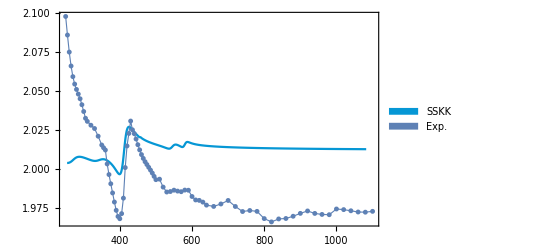

```mathematica
eps28DataRe=Table[{x,eps28Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp28sskk=Plot[partere282[h c/λ],{λ,h c/xmax,h c/xmin},
                  PlotStyle->blueUNAM,
                  PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.3]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.715,0.63}],
          
                  Evaluate[Sequence @@ plotStyling]];

plotpoints28sskk=ListPlot[{#[[1]],#[[2]]}&/@eps28DataRe,
                          PlotMarkers->{"●",5},
                          PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                           PlotStyle->Thickness[0.002],                                
                          
                          Joined->True,
                          Evaluate[Sequence @@ plotStyling]];

sskk28=Show[{interp28sskk,plotpoints28sskk}, FrameLabel->{{Style[MaTeX["\\text{Re}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
```

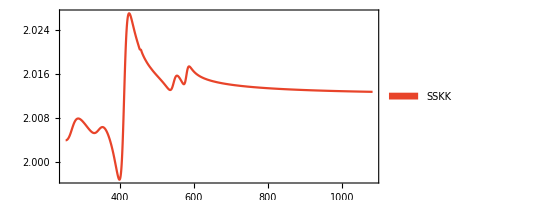

```mathematica
parteRe28=Plot[partere282[h c/λ],{λ,h c/xmax,h c/xmin},
                  PlotStyle->redUNAM,
                  PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.3]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.715,0.7}],
                                                
              
                  AspectRatio->1/2,
                   ImagePadding->{{90,10},{70,10}},
                  FrameLabel->{{Style[MaTeX["\\text{Re}\\{\\varepsilon(\\lambda)\\} "],Magnification->1.6],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.6],None}},
                  Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["parteRe28.svg",parteRe28]
```

parteRe28.svg

```mathematica
epsEritrocitosData28=Table[{w*0.2418,partere282[w],fit28tot[w]},{w,1,10,0.01}];
Export["epsEritrocitosData28.csv",epsEritrocitosData28]
```

epsEritrocitosData28.csv

```mathematica
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Funciones_dielectricas"]
epsEritrocitosData28lambda=Table[{h c/w,partere282[w],fit28tot[w]},{w,1,10,0.01}];
Export["epsEritrocitosData28lambda.csv",epsEritrocitosData28lambda]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Funciones_dielectricas

epsEritrocitosData28lambda.csv

#### Cálculo de la desviación de SSKK de los datos experimentales

```mathematica
Mean[Table[partere282[w]-eps28Re[w],{w,2,3.1,0.01}]]
```

0.019539

## Datos del review con SSKK

```mathematica
datosReview0=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\review_N_reported_KK.csv"];
datosReview1=Drop[datosReview0,1];
datosReview=Interpolation[Transpose[{datosReview1[[All,1]],datosReview1[[All,2]]}],InterpolationOrder->1]
datosFriebel0=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\review_N_reported_Friebel.csv"];
datosFriebel1=Drop[datosFriebel0,1];
datosFriebel=Interpolation[Transpose[{datosFriebel1[[All,1]],datosFriebel1[[All,2]]}],InterpolationOrder->1];
```

InterpolatingFunction[…]

```mathematica
listReview=Table[{l,datosReview[l]},{l,400,600}];
listFriebel=Table[{l,datosFriebel[l]},{l,400,600}];
```

```mathematica
Mean[Abs[listReview[[All,2]]-listFriebel[[All,2]]]]
```

0.0210577

```mathematica
h c/800
```

1.5498

```mathematica
eps28tot[x_]:=partere282[x] + I fit28tot[x]
ir28tot[x_]:=eps28tot[h c/x]
```

```mathematica
listsskk28=Table[{l,ir28tot[l]},{l,400,700}];
```

InterpolatingFunction::dmval: Input value {350.018} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

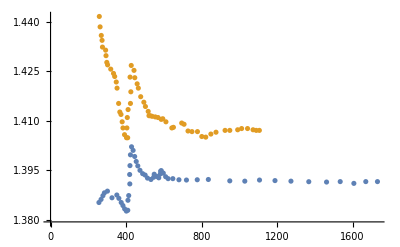

```mathematica
Show[ListPlot[{Transpose[{datosReview1[[All,1]],datosReview1[[All,2]]}],Transpose[{datosFriebel1[[All,1]],datosFriebel1[[All,2]]}]}],Plot[{Re[ir28tot[h c/x]]},{x,350,1250},PlotRange->All]]
```

```mathematica
h c/2.27
```

546.186

```mathematica
datosReview[350]
Re[ir28tot[h c/350]]
```

1.38752

InterpolatingFunction::dmval: Input value {350.} lies outside the range of data in the interpolating function. Extrapolation will be used.

5.36539×10^-14

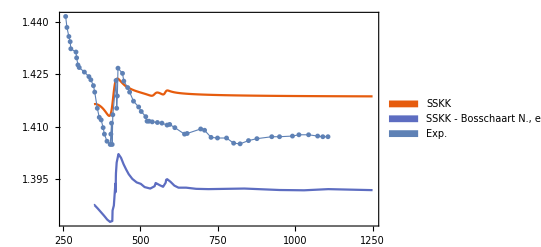

```mathematica
plotsskkYo=Plot[{Re[ir28tot[x]],datosReview[x]},{x,350,1250},
                   PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                               Style["SSKK - Bosschaart N., et al. 2013",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.53,0.87}],
                
                  Evaluate[Sequence @@ plotStyling]];

listplotsskkYo=ListPlot[Transpose[{datosFriebel1[[All,1]],datosFriebel1[[All,2]]}],
                          PlotMarkers->{"●",5},
                          PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                           PlotStyle->Thickness[0.002],                                
                          Joined->True,
                          Evaluate[Sequence @@ plotStyling]];

sskkComp=Show[{plotsskkYo,listplotsskkYo}, PlotRange->{{370,600},{Automatic,1.43}},FrameLabel->{{Style[MaTeX["\\text{Re}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Export["sskkComp.svg",sskkComp]
```

sskkComp.svg